```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 19 Kb

{Utilities`CleanSlate`,DocumentationSearch`,ResourceLocator`,VariationalMethods`,System`,Global`}

```mathematica
Clear[q]
q = { θ1[t] , θ2[t] }
```

{θ1[t],θ2[t]}

```mathematica
Clear[r] 
r = { l Sin[θ1[t]] + L Sin[θ2[t]] , -l Cos[θ1[t]] - L Cos[θ2[t]] }
```

{l Sin[θ1[t]]+L Sin[θ2[t]],-l Cos[θ1[t]]-L Cos[θ2[t]]}

```mathematica
D[r, t]
```

{l Cos[θ1[t]] θ1'[t]+L Cos[θ2[t]] θ2'[t],l Sin[θ1[t]] θ1'[t]+L Sin[θ2[t]] θ2'[t]}

```mathematica
D[r, t] . D[r, t]
```

(l Cos[θ1[t]] θ1'[t]+L Cos[θ2[t]] θ2'[t])^2+(l Sin[θ1[t]] θ1'[t]+L Sin[θ2[t]] θ2'[t])^2

```mathematica
D[r, t] . D[r, t]  // Expand
```

l^2 Cos[θ1[t]]^2 θ1'[t]^2+l^2 Sin[θ1[t]]^2 θ1'[t]^2+2 l L Cos[θ1[t]] Cos[θ2[t]] θ1'[t] θ2'[t]+2 l L Sin[θ1[t]] Sin[θ2[t]] θ1'[t] θ2'[t]+L^2 Cos[θ2[t]]^2 θ2'[t]^2+L^2 Sin[θ2[t]]^2 θ2'[t]^2

```mathematica
D[r, t] . D[r, t]  // Expand // Simplify
```

l^2 θ1'[t]^2+2 l L Cos[θ1[t]-θ2[t]] θ1'[t] θ2'[t]+L^2 θ2'[t]^2

```mathematica
Clear[T]
T = 1/2 M (D[r, t] . D[r, t]  // Expand // Simplify  ) +1/2( 1/3 M L^2 θ2'[t]^2)
```

1/6 L^2 M θ2'[t]^2+1/2 M (l^2 θ1'[t]^2+2 l L Cos[θ1[t]-θ2[t]] θ1'[t] θ2'[t]+L^2 θ2'[t]^2)

```mathematica
Clear[V] 
V = - M g (  l Cos[θ1[t]] + L Cos[θ2[t]] )
```

-g M (l Cos[θ1[t]]+L Cos[θ2[t]])

```mathematica
Clear[ℒ]
ℒ = T - V
```

g M (l Cos[θ1[t]]+L Cos[θ2[t]])+1/6 L^2 M θ2'[t]^2+1/2 M (l^2 θ1'[t]^2+2 l L Cos[θ1[t]-θ2[t]] θ1'[t] θ2'[t]+L^2 θ2'[t]^2)

```mathematica
D[ D[ ℒ , D[q[[1]], t] ] , t] - D[ ℒ , q[[1]] ] // Expand // Simplify 
D[ D[ ℒ , D[q[[2]], t] ] , t] - D[ ℒ , q[[2]] ] // Expand // Simplify
```

l M (g Sin[θ1[t]]+L Sin[θ1[t]-θ2[t]] θ2'[t]^2+l θ1''[t]+L Cos[θ1[t]-θ2[t]] θ2''[t])

1/3 L M (3 g Sin[θ2[t]]-3 l Sin[θ1[t]-θ2[t]] θ1'[t]^2+3 l Cos[θ1[t]-θ2[t]] θ1''[t]+4 L θ2''[t])

```mathematica
Table[
D[ D[ ℒ , D[q[[i]], t] ] , t] - D[ ℒ , q[[i]] ],
{ i, 1, 2 } ] // TableForm
```

g l M Sin[θ1[t]]+l L M Sin[θ1[t]-θ2[t]] θ1'[t] θ2'[t]+1/2 M (-2 l L Sin[θ1[t]-θ2[t]] (θ1'[t]-θ2'[t]) θ2'[t]+2 l^2 θ1''[t]+2 l L Cos[θ1[t]-θ2[t]] θ2''[t])
g L M Sin[θ2[t]]-l L M Sin[θ1[t]-θ2[t]] θ1'[t] θ2'[t]+1/3 L^2 M θ2''[t]+1/2 M (-2 l L Sin[θ1[t]-θ2[t]] θ1'[t] (θ1'[t]-θ2'[t])+2 l L Cos[θ1[t]-θ2[t]] θ1''[t]+2 L^2 θ2''[t])

```mathematica
Clear[eqs]
eqs = EulerEquations[ ℒ , q , t ] ;
eqs // TableForm
```

-l M (g Sin[θ1[t]]+L Sin[θ1[t]-θ2[t]] θ2'[t]^2+l θ1''[t]+L Cos[θ1[t]-θ2[t]] θ2''[t])==0
-1/3 L M (3 g Sin[θ2[t]]-3 l Sin[θ1[t]-θ2[t]] θ1'[t]^2+3 l Cos[θ1[t]-θ2[t]] θ1''[t]+4 L θ2''[t])==0

```mathematica
Clear[ics]
ics = { 
θ1[0] == 0.2 ,
θ1'[0] == 0.2 ,
θ2[0] == 0.2 , 
θ2'[0] == 0.2 
} ;
ics // TableForm
```

θ1[0]==0.2
θ1'[0]==0.2
θ2[0]==0.2
θ2'[0]==0.2

```mathematica
Clear[parameters]
parameters = { 
M-> 10 ,
g-> 9.8,
L-> 2,
l-> 4
} ;
parameters // TableForm
```

M→10
g→9.8
L→2
l→4

```mathematica
eqs //. parameters // TableForm
```

-40 (9.8 Sin[θ1[t]]+2 Sin[θ1[t]-θ2[t]] θ2'[t]^2+4 θ1''[t]+2 Cos[θ1[t]-θ2[t]] θ2''[t])==0
-20/3 (29.4 Sin[θ2[t]]-12 Sin[θ1[t]-θ2[t]] θ1'[t]^2+12 Cos[θ1[t]-θ2[t]] θ1''[t]+8 θ2''[t])==0

```mathematica
Clear[solution]
solution = 
NDSolve[ Union[ eqs //. parameters , ics ] , q , { t, 0, 10 } ]
```

{{θ1[t]→InterpolatingFunction[…][t],θ2[t]→InterpolatingFunction[…][t]}}

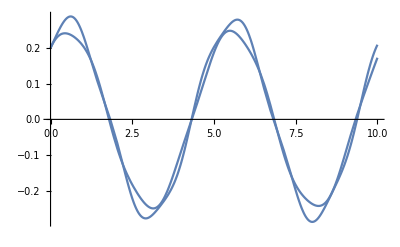

```mathematica
Plot[ q  //.  solution , { t, 0, 10 } ]
```

```mathematica
Exit[]
Quit[]
```